```mathematica
open
```

## Oscillations and Waves Exam 3

## April 29, 2025

## This is a short exam designed to checkpoint your knowledge of the core of the Wolfram Language. EIWL3 Sections 25-34, and Sections 38-41 were when we got to the grammar and a significantly more advanced understanding of the core of the language. I have attempted to create representative problems covering all of these sections.

## Directions: After downloading this notebook, rename it with your first name in the filename. E.g., Eli-Exam3.nb, Harper-Exam3.nb, Hexi-Exam3.nb, Jeremy-Exam3.nb, Rania-Exam3.nb, Tahm-Exam3.nb, or Walker-Exam3.nb. Then disconnect from the wifi and work the exam. Save your notebook early and often so that you don’t lose work in progress. You may refer to your downloaded copies of EIWL3, and anything else we developed in the course, including your cheat sheets, but not to any other web resources. When you are done, save your notebook one last time, re-join the wifi, and then email it to me. The exam is designed to only require about 45 minutes, but if you need a full hour, that is ok. Everyone will stop at the one hour mark.

### 1. Map and // à la EIWL3 Section 25

#### (a)

Use Map with a levelspec to put a frame around each individual number in this array:

```mathematica
Array[Plus,{10,10}]
```

#### (b)

Copy what you did in (a), but for this part, also turn the result into a grid using Grid using the “as an afterthought” syntax:

```mathematica
Array[Plus,{10,10}]
```

### 2. Pure Anonymous Functions à la EIWL3 Section 26

#### (a)

Use the # and & notation to create an anonymous function that cubes whatever is given it, and then use /@ to apply it to the list {1, 2, 3, 4, 5}:

```mathematica
#^3&/@{1,2,3,4,5}
```

{1,8,27,64,125}

#### (b)

Use the #1, #2, and & notation to create an anonymous function divides its first argument by its second argument. Combine this with Apply and a levelspec to apply the function to {{1,2},{2,3},{3,4},{4,5}}. Once you have this right, you will get {1/2,2/3,3/4,4/5} .

```mathematica
Apply[#1/#2 &, {{1,2},{2,3},{3,4},{4,5}},2]
```

{1/2,2/3,3/4,4/5}

### 3. Applying Functions Repeatedly à la EIWL3 Section 27

#### (a)

Use Nest to apply Factorial twice to {1, 2, 3, 4}. If you have this right, 620,448,401,733,239,439,360,000 will be part of your answer.

```mathematica
Nest[Factorial,{1,2,3,4},2]
```

{1,2,720,620448401733239439360000}

#### (b)

Use NestList to apply Factorial three times to {1, 2, 3} , as well as showing the intermediate results. If you have this right, you will have an insanely large result at the third step. Do not go any higher, or I do not know what will happen to your computer.

```mathematica
NestList[Factorial,{1,2,3},3]
```

{{1,2,3},{1,2,6},{1,2,720},{1,2,2601218943565795100204903227081043611191521875016945785727541837850835631156947382240678577958130457082619920575892247259536641565162052015873791984587740832529105244690388811884123764341191951045505346658616243271940197113909845536727278537099345629855586719369774070003700430783758997420676784016967207846280629229032107161669867260548988445514257193985499448939594496064045132362140265986193073249369770477606067680670176491669403034819961881455625195592566918830825514942947596537274845624628824234526597789737740896466553992435928786212515967483220976029505696699927284670563747137533019248313587076125412683415860129447566011455420749589952563543068288634631084965650682771552996256790845235702552186222358130016700834523443236821935793184701956510729781804354173890560727428048583995919729021726612291298420516067579036232337699453964191475175567557695392233803056825308599977441675784352815913461340394604901269542028838347101363733824484506660093348484440711931292537694657354337375724772230181534032647177531984537341478674327048457983786618703257405938924215709695994630557521063203263493209220738320923356309923267504401701760572026010829288042335606643089888710297380797578013056049576342838683057190662205291174822510536697756603029574043387983471518552602805333866357139101046336419769097397432285994219837046979109956303389604675889865795711176566670039156748153115943980043625399399731203066490601325311304719028898491856203766669164468791125249193754425845895000311561682974304641142538074897281723375955380661719801404677935614793635266265683339509760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}

### 4. Conditionals à la EIWL3 Section 28

#### (a)

Use PrimeQ to generate a True or False list that is twenty elements long, and expresses which numbers in Range[20] are prime:

```mathematica
PrimeQ/@Range[20]
```

{False,True,True,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,True,False}

#### (b)

Combine PrimeQ with Select to only list the numbers in Range[20] that are prime:

```mathematica
Select[Range[20],PrimeQ]
```

{2,3,5,7,11,13,17,19}

### 5. Rearranging Lists à la EIWL3 Section 30

#### (a)

Use Transpose and one of the levelspec options to turn {{{1, uno},{2,dos},{3,tres}},{{4,quattro},{5,cinco},{6,seis}}} into {{{1,2,3},{uno,dos,tres}},{{4,5,6},{quattro,cinco,seis}}}

```mathematica
Transpose[{{{1, uno},{2,dos},{3,tres}},{{4,quattro},{5,cinco},{6,seis}}},{1,3,2}]
```

{{{1,2,3},{uno,dos,tres}},{{4,5,6},{quattro,cinco,seis}}}

```mathematica
{{{1,2,3},{dog,cat,horse}},{{4,5,6},{cuatro,cinco,seis}}}
```

#### (b)

Use Flatten and a levelspec to turn {{{1, uno},{2,dos},{3,tres}},{{4,quattro},{5,cinco},{6,seis}}} into {{1,uno},{2,dos},{3,tres},{4,quattro},{5,cinco},{6,seis}}

```mathematica
Flatten[{{{1, uno},{2,dos},{3,tres}},{{4,quattro},{5,cinco},{6,seis}}},1]
```

{{1,uno},{2,dos},{3,tres},{4,quattro},{5,cinco},{6,seis}}

### 6. Parts of Lists à la EIWL3 Section 31

#### (a)

Use the magical All position to {{{1, uno},{2,dos},{3,tres}},{{4,quattro},{5,cinco},{6,seis}}} into {{uno,dos,tres},{quattro,cinco,seis}}

#### (b)

Use a magical negative positional argument to turn  {{uno,dos,tres},{quattro,cinco,seis}} into  {quattro,cinco,seis} and then use Take with a magical negative argument so that you only get {cinco,seis}.

```mathematica
Take[{{uno,dos,tres},{quattro,cinco,seis}}[[-1]],-2]
```

{cinco,seis}

### 7. Patterns à la EIWL3 Section 32

#### (a)

Use pattern matching to find the lists that begin and end with the same thing in this  list of lists: 

{
{“a”, “l”, “u”, “l”, “a”}, 
{“a”, “l”, “o”, “h”, “a”},
 {“a”, “r”, “a”, “r”, “a”}, 
 {“b”, “o”, “n”, “u”, “s”},
 {“c”, “i”, “v”, “i”, “c”},
 {“d”, “e”, “b”, “e”, “d”}, 
 {“e”, “l”, “b”, “o”, “w”}
}

```mathematica
Cases[{{"a","l","u","l","a"},{"a","l","o","h","a"},{"a","r","a","r","a"},{"b","o","n","u","s"},{"c","i","v","i","c"},{"d","e","b","e","d"},{"e","l","b","o","w"},{"z","z"}
},{x_,___,x_}]
```

{{a,l,u,l,a},{a,l,o,h,a},{a,r,a,r,a},{c,i,v,i,c},{d,e,b,e,d},{z,z}}

#### (b)

Look up BlankNullSequence and figure out how to alter the pattern you used in Part (a) so that {z,z} is included in your result.

### 8. Assigning Names à la EIWL3 Section 39

#### (a)

Use Module[] to compute x=Factorial[10] only once, and then produce {x,x^2, x^3}.

```mathematica
Module[{x=Factorial[10]},{x,x^2,x^3}]
```

{3628800,13168189440000,47784725839872000000}

#### (b)

Inside a module, let rangeSquared=Range[10]^2, and then make a list line plot of rangeSquared joined with Reverse[rangeSquared]:

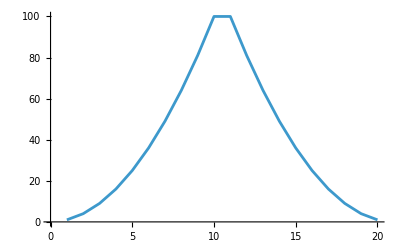

```mathematica
Module[{rangeSquared=Range[10]^2},ListLinePlot[Join[rangeSquared,Reverse[rangeSquared]]]]
```

### 9. Immediate and Delayed Values à la EIWL3 Section 39

#### (a)

Make a one-character change to this expression, so that it produces four different powers of the same number:

```mathematica
Module[{x:=RandomInteger[10]},{x,x^2,x^3,x^4}]
```

{3,16,64,6561}

#### (b)

Make a one-character change to this expression, so that it produces five different color disks:

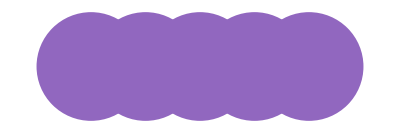

```mathematica
Module[{color=RandomColor[]},Graphics[Table[Style[Disk[{i,0}],color],{i,5}]]]
```

### 10. Defining your own functions à la EIWL3 Section 40

#### (a)

Define a function f that takes a list of three elements and puts them in a list of lists that contains all 6 possible orderings:

```mathematica
f[a_,b_,c_]:=Permutations[{a,b,c}]
```

Test your function as f[1,2,3] and make sure it gets {{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
f[1,2,3]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

#### (b)

Define a function g that gives 1 for g[0], and gives n*g[n-1] for any integer greater than 0. Don’t use an If statement!

```mathematica
g[0]=1
```

1

```mathematica
g[n_]:=n g[n-1]
```

Test your function as g[6] and make sure it gets 720.

```mathematica
g[6]
```

720